# Mathematica Plot Gallery

## Standard Plots

Function Plots

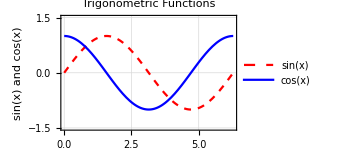

```mathematica
a=Plot[{Sin[x],Cos[x]},{x,0,2Pi},
		PlotStyle->{{Red,Dashed,Thick},{Blue,Thick}},
		PlotLabel->"Trigonometric Functions",
		Frame->True,
		FrameLabel->{"angle","sin(x) and cos(x)"},
		GridLines->Automatic,
		PlotRange->{{0,2Pi},{-1.5,1.5}},
		PlotLegends->{"sin(x)","cos(x)"},
		ImageSize->250]
```

```mathematica
GraphicsGrid[{{a,a},{a,a}}];
```

ListLinePlot

```mathematica
RandomVariate[NormalDistribution[0,1]]
```

0.641918

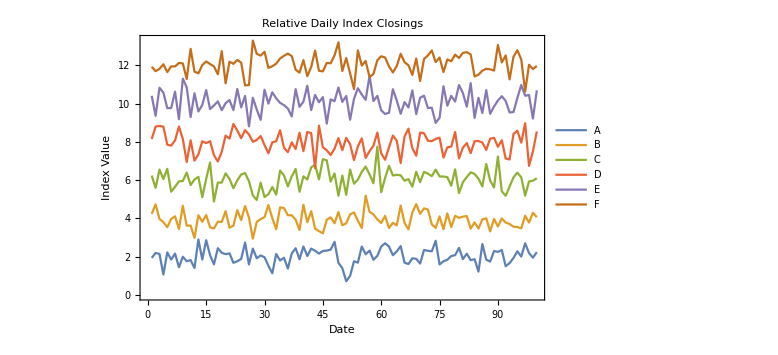

```mathematica
a= Block[{data},
	data=Table[Table[i+RandomVariate[NormalDistribution[i+0,0.5]],100],{i,6}];
	ListLinePlot[data,
		PlotLabel->"Relative Daily Index Closings",
		LabelStyle-> Directive[Bold, Purple],
		PlotLegends->Placed[{"A","B","C","D","E","F"},Right,Framed[#]&],
		Frame->True,
		FrameLabel->{"Date","Index Value"},
		ImageSize->Large]]
```

```mathematica
Labeled[a[[1]],a[[2,1]],Left];
```

ListPlot

```mathematica
Block[{data},
	data=Table[Table[i+RandomVariate[NormalDistribution[1,1]],100],{i,6}];
	ListPlot[data,
		PlotLabel->"Relative Daily Index Closings",
		PlotMarkers->{"❤",".b4∀`","(*.b4 `*)","◡̈⃝", "♡","꒰❃.b4◡`❃꒱"},
		LabelStyle-> Directive[Bold, Purple],
		PlotLegends->Placed[{"A","B","C","D","E","F"},Right,Framed[#]&],
		Frame->True,
		FrameLabel->{"Date","Index Value"},
		ImageSize->Large]]
```

-Graphics-

ContourPlot

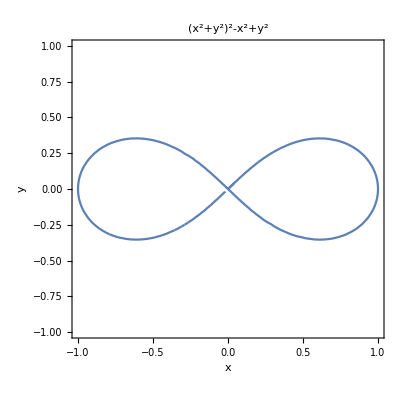

```mathematica
ContourPlot[(x^2+y^2)^2-x^2+y^2==0,{x,-1,1},{y,-1,1},
	PlotLabel->(x^2 + y^2)^2 - x^2 + y^2,
	Frame->True,
	FrameLabel->{"x","y"}]
```

```mathematica
FullForm[x^2]
```

Power[x,2]

```mathematica
Power[x,2]
```

x^2

PieChart

```mathematica
PieChart[{1,2,3,4,5},SectorOrigin->{Automatic,1},
		ChartLabels->{"a","b","c","d","(๑^ω^๑)"}]
```

-Graphics-

```mathematica
PieChart[{{1,2,3,4,5},{9,4,2,1,1}},ChartLabels->{"a","b","c","d","(๑^ω^๑)"}]
```

-Graphics-

```mathematica
PieChart[RandomReal[3,400],ChartStyle->"Rainbow",
		ChartBaseStyle->EdgeForm[None]]
```

-Graphics-

```mathematica
PieChart[{{1,1,1},{1,1,1},{1,1,1}}]
```

-Graphics-

```mathematica
PieChart[{{1,1,1,1},{1,1,1,1}}]
```

-Graphics-

```mathematica
FullForm[1]
```

Quantity[1,"Meters"]

## Customizing Plots

## Advanced Plots